# Graphs and networks

Kyungwon Chun
Sep. 23, 2019

```mathematica
<<SymbolicComputing`

boilerplateTemplate=StringTemplate["This notebook depends on Mathematica `ver` and MathSymbolica `scVer`. Also, the contents reflect the last execution on `date`."];
Print[boilerplateTemplate[<|"scVer"->$SCVersion,"ver"->$Version, "date"->DateString[]|>]]
```

## Basic Topics

A connection from 1 to 2 is

```mathematica
1->2//FullForm
```

Rule[1,2]

We can construct a very simple graph using a few conections.

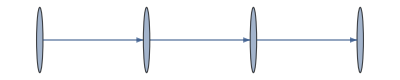

```mathematica
Graph@{1->2,2->3,3->4}
```

@ is Prefix and the above expression is equivalent to the following one:

```mathematica
Graph[{1->2,2->3,3->4}]
```

-Graphics-

It is awkward to make a graph without node labels.

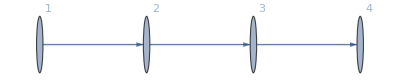

```mathematica
Graph[{1->2,2->3,3->4},VertexLabels->Automatic]
```

If we add one more connection which connects 4 from 1.

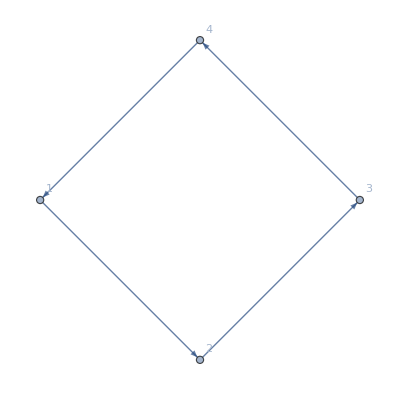

```mathematica
Graph[{1->2,2->3,3->4,4->1},VertexLabels->Automatic]
```

Keep going to add more connections:

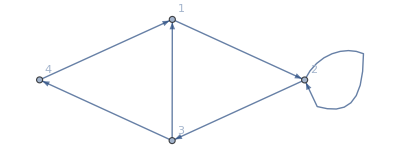

```mathematica
Graph[{1->2,2->3,3->4,4->1,3->1,2->2},VertexLabels->Automatic]
```

We can plot the graph with different layout.

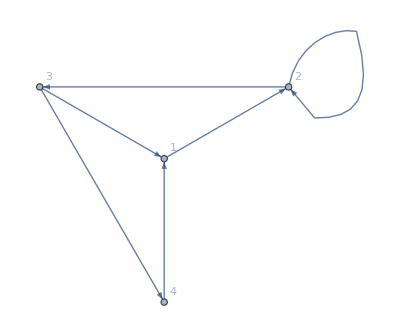

```mathematica
Graph[{1->2,2->3,3->4,4->1,3->1,2->2},VertexLabels->Automatic,GraphLayout->"RadialEmbedding"]
```

Wolfram language provides us the way to find the shortest path from one node to the other.

```mathematica
FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2},VertexLabels->Automatic,GraphLayout->"RadialEmbedding"],4,2]
```

{4,1,2}

Let’s make a full connected graph.

```mathematica
Table[i->j,{i,3},{j,3}]
```

{{1→1,1→2,1→3},{2→1,2→2,2→3},{3→1,3→2,3→3}}

But, the following expression does not plot the graph.

```mathematica
Graph@Table[i->j,{i,3},{j,3}]
```

Graph[{{1→1,1→2,1→3},{2→1,2→2,2→3},{3→1,3→2,3→3}}]

The following expresison works well.

```mathematica
Graph@{1->1,1->2,1->3,2->1,2->2,2->3,3->1,3->2,3->3}
```

-Graphics-

Let’s look at the structure of given data.

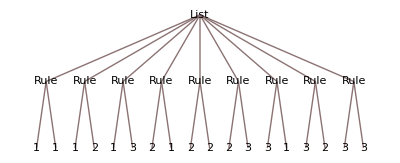

```mathematica
{1->1,1->2,1->3,2->1,2->2,2->3,3->1,3->2,3->3}//TreeForm
```

But, the data in our hand, has a hierarchy structure of List.

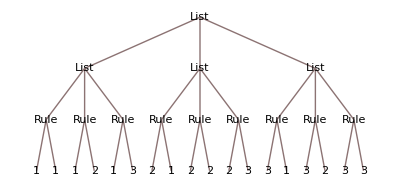

```mathematica
{{1->1,1->2,1->3},{2->1,2->2,2->3},{3->1,3->2,3->3}}//TreeForm
```

Flatten provides a way to remove this hierarchy of List.

```mathematica
{{1->1,1->2,1->3},{2->1,2->2,2->3},{3->1,3->2,3->3}}//Flatten
```

Now, we can plot our full connected graph.

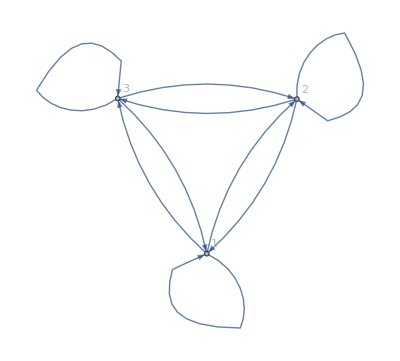

```mathematica
Graph[Flatten@Table[i->j,{i,3},{j,3}],VertexLabels->Automatic]
```

Let’s increase the number of nodes in our full connected graph.

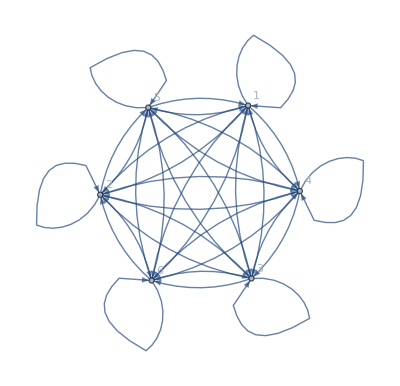

```mathematica
Graph[Flatten@Table[i->j,{i,6},{j,6}],VertexLabels->Automatic]
```

We can change our graph to a undirected graph.

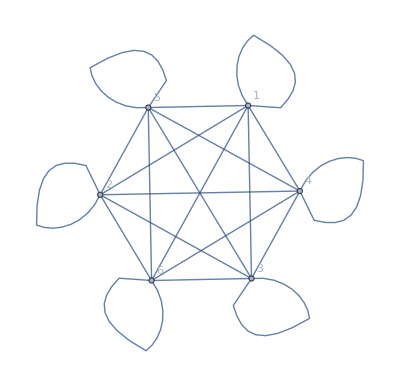

```mathematica
UndirectedGraph[Flatten@Table[i->j,{i,6},{j,6}],VertexLabels->Automatic]
```

A random graph with 11 nodes can be generated easily.

```mathematica
Graph@Table[RandomInteger[10]->RandomInteger[10],20]
```

-Graphics-

We can add node labels, but re-evaluation of the expression changes the connections of graph as the effect of RandomInteger.

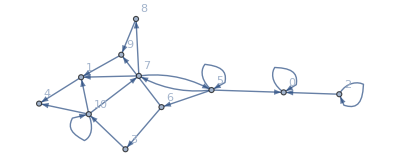

```mathematica
Graph[Table[RandomInteger[10]->RandomInteger[10],20],VertexLabels->Automatic]
```

We can confirm the randomized connections at one sight.

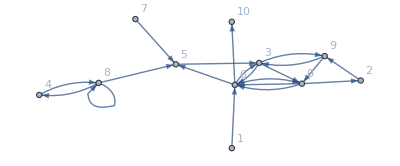
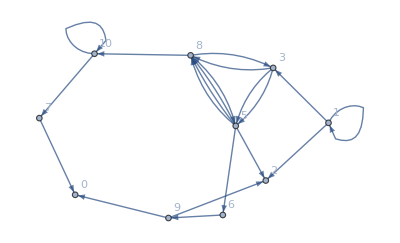
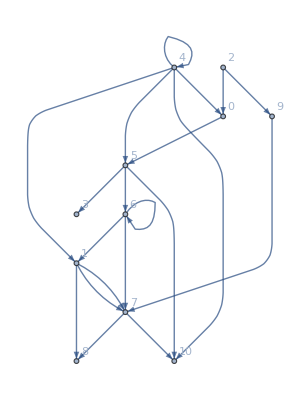
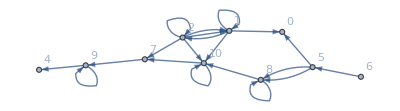
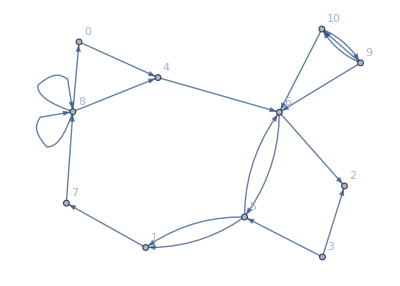
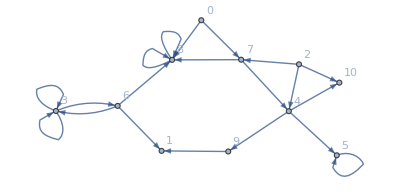

```mathematica
Table[Graph[Table[RandomInteger[10]->RandomInteger[10],20],VertexLabels->Automatic],6]
```

Let’s choose one of the graph in the above output, then copy and paste it at the next input cell. Then we can look for a closely connected cluster in them.

```mathematica
CommunityGraphPlot@-Graphics-
```

-Graphics-

## Exercises

Make a graph with 4 nodes in which every node is connected.

```mathematica
Graph@Flatten@Table[i->j,{i,4},{j,4}]
```

-Graphics-

Use Table and Flatten to get {1, 2, 1, 2, 1, 2}

```mathematica
Flatten@Table[{1,2},3]
```

{1,2,1,2,1,2}

Generate a graph with 100 nodes, each connecting to two randomly chosen nodes.

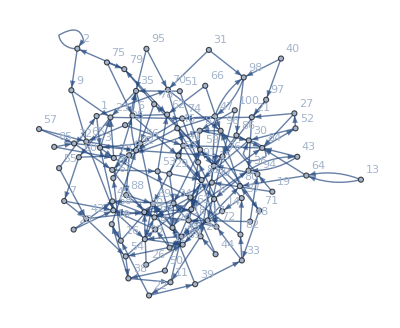

```mathematica
Graph[Flatten@Table[{i->RandomInteger[{1,100}],i->RandomInteger[{1,100}]},{i,100}],VertexLabels->Automatic]
```

## Intermediate Topics

This makes a list of the results of nesting f up to 4 times:

```mathematica
NestList[f,x,4]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]]}

We can implement Range[16] using NestList:

```mathematica
NestList[#+1&,1,15]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

We can implement 2^15 using NestList:

```mathematica
NestList[2*#&,1,15]//Last
```

32768

or

```mathematica
Nest[2*#&,1,15]
```

32768

Start from x, then repeatedly connect to the list of nodes obtained by applying the function:

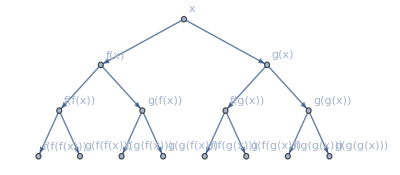

```mathematica
NestGraph[{f[#],g[#]}&,x,3,VertexLabels->Automatic]
```

Repeatedly apply a numerical function to form another tree structure:

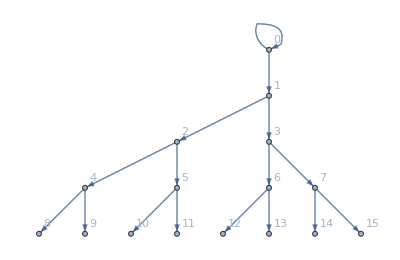

```mathematica
NestGraph[{2#,2#+1}&,0,4,VertexLabels->Automatic]
```

The following expression returns a list of countries that border to Switzerland.

```mathematica
Entity["Country","Switzerland"]["BorderingCountries"]
```

{Austria,France,Germany,Italy,Liechtenstein}

“Crawl” outward 2 steps from Switzerland, connecting each country to all those that border it:

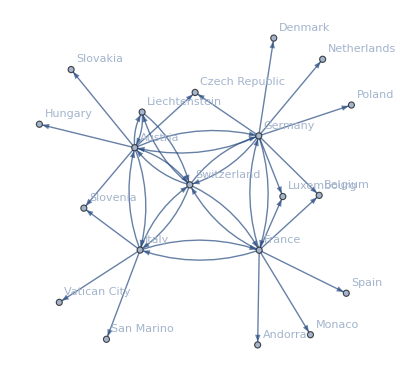

```mathematica
NestGraph[#["BorderingCountries"]&,Entity["Country","Switzerland"],2,VertexLabels->Automatic]
```

WordList gives a list of most commonly used words:

```mathematica
WordList[Language->"English"]
```

{a,aah,aardvark,aback,abacus,abaft,abalone,abandon,abandoned,39158,zoology,zoom,zoophyte,zounds,zucchini,zwieback,zydeco,zygote,zygotic}
 |  |  |  |

We can find the words whcih can get with smallest changes from “hello.”

```mathematica
Nearest[WordList[Language->"English"],"hello",3]
```

{hello,cello,hallo}

```mathematica
EditDistance[#,"hello"]&/@{"hello","cello","hallo"}
```

{0,1,1}

Create a network of nearby words iwth respect to 3-letter changes:

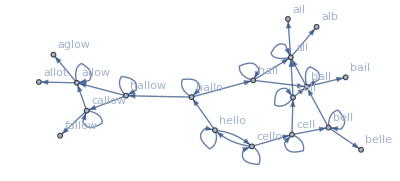

```mathematica
NestGraph[Nearest[WordList[Language->"English"],#,3]&,"hello",4,VertexLabels->Automatic]
```

## Advanced Topics

Threads → across the lements of two lists:

```mathematica
Thread[{1,2,5,7,9}->{2,4,6,8,10}]
```

{1→2,2→4,5→6,7→8,9→10}

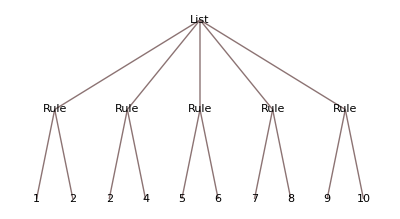

```mathematica
{1->2,2->4,5->6,7->8,9->10}//TreeForm
```

Threads List over any objects with head Rule that appear in arguments of List. The result is reversing the former expression.

```mathematica
Thread[{1->2,2->4,5->6,7->8,9->10},Rule]
```

{1,2,5,7,9}→{2,4,6,8,10}

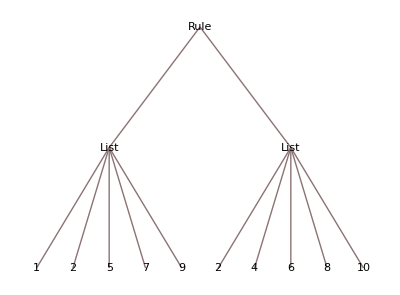

```mathematica
{1,2,5,7,9}->{2,4,6,8,10}//TreeForm
```

If we want to select elements, satisfying a certain condition:

```mathematica
{-1,1,2.2,3,4.5,5};
Select[%,Positive]
```

{1,2.2,3,4.5,5}

If we want to select integers geater than 4:

```mathematica
{-1,1,2.2,3,4.5,5};
Select[%,#>4&]
Cases[%,_Integer]
```

{4.5,5}

{5}

When you want to change the header of expression, use Apply, @@:

```mathematica
f@@{x,y,z}
```

f[x,y,z]

```mathematica
{x,y,z}//FullForm
```

List[x,y,z]

```mathematica
f[x,y,z]
```

f[x,y,z]

```mathematica
f@@{x,y,z}
```

f[x,y,z]

If you know the underlining principle, you can try other method which performs the same job.

```mathematica
{x,y,z}/.List->f
```

f[x,y,z]

Since there are lots of functions that generate lists, it’s often convenient to build up structures as lists even if eventually one needs to replace the lists with other functions.

```mathematica
Plus@@{1,1,1,1}
```

4

```mathematica
Plus[1,1,1,1]
```

4

This turns a list into a rule:

```mathematica
#1->#2&@@{x,y}
```

x→y

```mathematica
Rule@@{x,y}
```

x→y

```mathematica
List[x,y]
```

```mathematica
Rule[x,y]
```

A surprisingly common situation is to have a list of lits, and to want to replace the inner lists with some function. It’s possible to do this with @@ and /@. But @@@ provides a convenient direct way to do it.

```mathematica
{Rule@@{x,y},Rule@@{y,z},Rule@@{1,2}}
```

{x→y,y→z,1→2}

```mathematica
Rule@@#&/@{{x,y},{y,z},{1,2}}
```

{x→y,y→z,1→2}

```mathematica
Map[Rule@@#&,{{x,y},{y,z},{1,2}}]
```

{x→y,y→z,1→2}

```mathematica
Rule@@@{{x,y},{y,z},{1,2}}
```

{x→y,y→z,1→2}

This generates a list of characters:

```mathematica
Characters@"antidisestablishmentarianism"
```

{a,n,t,i,d,i,s,e,s,t,a,b,l,i,s,h,m,e,n,t,a,r,i,a,n,i,s,m}

This generates a list of paris of characters:

```mathematica
Partition[Characters@"antidisestablishmentarianism",2,1]
```

{{l,h},{h,k},{k,a},{a,s},{s,d},{d,k},{k,f},{f,g},{g,w},{w,u},{u,i},{i,e},{e,b},{b,v},{v,l},{l,a},{a,i},{i,s},{s,d},{d,f},{f,h},{h,e},{e,b},{b,q},{q,l},{l,i},{i,d},{d,h},{h,v},{v,a},{a,s},{s,d},{d,j},{j,k},{k,f},{f,b},{b,q},{q,u},{u,d}}

Tur this into a list of rules:

```mathematica
Rule@@@Partition[Characters@"antidisestablishmentarianism",2,1]
```

{a→n,n→t,t→i,i→d,d→i,i→s,s→e,e→s,s→t,t→a,a→b,b→l,l→i,i→s,s→h,h→m,m→e,e→n,n→t,t→a,a→r,r→i,i→a,a→n,n→i,i→s,s→m}

Form a transition graph showing how letters follow each other:

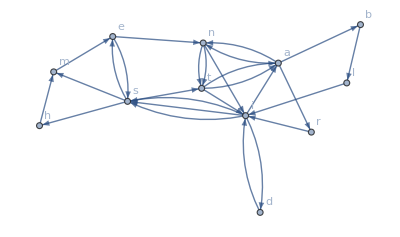

```mathematica
Graph[Rule@@@Partition[Characters@"antidisestablishmentarianism",2,1],VertexLabels->Automatic]
```